## Interfacing with Armadillo

This notebook demonstrates how to interface with the Armadillo linear algebra library.

```mathematica
Needs["LTemplate`"]
SetDirectory@NotebookDirectory[];
```

```mathematica
template=
LClass["Arma",
{
LFun["inv",{{Real,2,"Constant"}},{Real,2}],
LFun["eigs",{{LType[SparseArray,Real,2],"Constant"},Integer},{Complex,1}],
LFun["sprandu",{Integer,Integer,Real},LType[SparseArray,Real]],
LFun["solve",{{Real,2,"Constant"},{Real,1,"Constant"}},{Real,1}],
LFun["print",{{Real,2,"Constant"}},"Void"],
LFun["printSparse",{{LType[SparseArray,Real,2],"Constant"}},"Void"]
}
];
```

When using an additional library like Armadillo, it is typically necessary to specify include paths, library paths, and libraries to link against. Adjust the CompileTemplate options below according to where you have installed Armadillo.

On OS X, Armadillo can optionally make use of the Accelerate framework, which is included in the compile options below.

```mathematica
CompileTemplate[template,
"IncludeDirectories"->{"/opt/local/include"},
"LibraryDirectories"->{"/opt/local/lib"},
"Libraries"->{"armadillo"},
"CompileOptions"->{"-std=c++14","-framework Accelerate"}
]
```

Current directory is: /Users/szhorvat/Repos/LTemplate/LTemplate/Documentation/Examples/Armadillo

Unloading library Arma ...

Generating library code ...

Compiling library code ...

/Users/szhorvat/Library/Mathematica/SystemFiles/LibraryResources/MacOSX-x86-64/Arma.dylib

```mathematica
LoadTemplate[template]
```

```mathematica
arma=Make[Arma]
```

Arma[1]

Let us create a large random matrix ...

```mathematica
m=RandomReal[1,{500,500}];
```

... and compute its inverse.

```mathematica
im=arma@"inv"[m];//RepeatedTiming
```

RepeatedTiming[Null]

```mathematica
im2=Inverse[m];//RepeatedTiming
```

RepeatedTiming[Null]

Armadillo can be set up to output messages to any stream. In this example, it is set up to output to mma::mout. This way the messages appear directly in the notebook in case of an error.

Exceptions are also caught by LTemplate and their description is included into the message.

```mathematica
arma@"inv"[RandomReal[1,{5,6}]]
```

error: inv(): given matrix must be square sized

LTemplate::error: "Unknown exception caught in Arma::inv(). The library may be in an inconsistent state. It is recommended that you restart the kernel now to avoid instability.\ninv(): given matrix must be square sized"

LibraryFunctionError[LIBRARY_FUNCTION_ERROR,6]

Compute the first few eigenvalues (those largest in magnitude) of a sparse matrix.

```mathematica
sparse=N@AdjacencyMatrix@RandomGraph[{10,25},DirectedEdges->True];
```

```mathematica
arma@"eigs"[sparse,5]
```

{2.44815+0. ⅈ,-1.15439+0.67747 ⅈ,-1.15439-0.67747 ⅈ,-1.+0. ⅈ,0.82243-0.181011 ⅈ}

```mathematica
Eigenvalues[sparse,5]
```

{2.44815+0. ⅈ,-1.15439+0.67747 ⅈ,-1.15439-0.67747 ⅈ,-1.+0. ⅈ,0.82243+0.181011 ⅈ}

Create a 10×20 sparse matrix with density 0.1 and uniformaly distributed random entries between 0 and 1.

```mathematica
arma@"sprandu"[10,20,0.1]
```

SparseArray[<20>, {10, 20}]

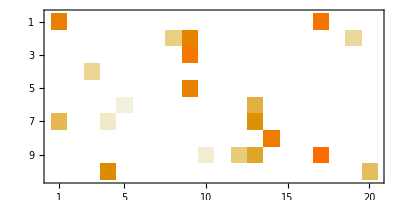

```mathematica
MatrixPlot[%]
```

Solve a linear equation.

```mathematica
arma@"solve"[({{1, 6, -3}, {5, -2, -2}, {1, 1, 1}}),{2,0,1}]
```

{0.285714,0.428571,0.285714}

Compare the result with LinearSolve.

```mathematica
N@LinearSolve[({{1, 6, -3}, {5, -2, -2}, {1, 1, 1}}),{2,0,1}]
```

{0.285714,0.428571,0.285714}

Try to solve a singular system.

```mathematica
arma@"solve"[{{1,1},{1,1}},{6,15}]
```

warning: solve(): system seems singular; attempting approx solution

{5.25,5.25}

Print an Armadillo matrix directly to the notebook:

```mathematica
arma@"print"[{{1,2},{2,3}}]
```

1.0000   2.0000
   2.0000   3.0000

Print the explicitly stored entries of a sparse matrix:

```mathematica
arma@"printSparse"[AdjacencyMatrix@RandomGraph[{5,5}]]
```

[matrix size: 5x5; n_nonzero: 10; density: 40.00%]

     (2, 0)         1.0000
     (3, 0)         1.0000
     (4, 0)         1.0000
     (2, 1)         1.0000
     (0, 2)         1.0000
     (1, 2)         1.0000
     (4, 2)         1.0000
     (0, 3)         1.0000
     (0, 4)         1.0000
     (2, 4)         1.0000